```mathematica
(************************Program Mahdi Molavi************************)
(********* git hub : https://github.com/mahdipc/mathematica*************)
```

```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
P[mm_,X_]:=Module[{x=X},
Return[LegendreP[mm,x]];
];
ψ[Ι_,J_,X_]:=Module[{i1=Ι,j1=J,xX=X},
nhs=2i1-1;
Return[Piecewise[{{√((2j1+1)/2)2^(k/2)P[j1,2^k xX-nhs],  (nhs-1)/2^k≤ xX && xX<(nhs+1)/2^k }},0]];
];
Ψ[X_]:=Module[{x=X},
Return[Flatten[Table[ψ[i,j,x],{i,1,2^(k-1)},{j,0,M-1}]]];
];
b[Ι_,X_]:=Module[{i=Ι,x=X},
Return[Piecewise[{{1, i h≤ x &&  x< (i+1)h}},0]];
];
B[X_]:=Module[{x=X},
Return[Table[b[i,x],{i,0,mh-1}]];
];
Φ[]:=Module[{},
Return[1/h Table[∫_0^1 Ψ[y]⟦i⟧B[y]⟦j⟧ⅆy,{i,1,mh},{j,1,mh}]];
];
ζ[Kk_,α_]:=Module[{kk=Kk},
Return[(kk+1)^(α+1)-2 kk^(α+1)+(kk-1)^(α+1)];
];
F[α_]:=Module[{},
A=IdentityMatrix[mh];
For[i=1,i< mh,i++,
For[j=i+1,j≤ mh,j++,
A⟦i,j⟧=ζ[j-i,α];
];
];
Return[h^α 1/Gamma[α+2] A];
];
P[α_]:=Module[{},
Return[Φ[].F[α].Inverse[Φ[]]];
];
𝔈[]:=Module[{},
Return[Simplify[𝒞[].P[α].Φ[]]];
];
𝒟[X_]:=Module[{x=X},
Aa=Table[Piecewise[{{∫_(jj/mh)^((jj+1)/mh) (B[s]⟦jj+1⟧)/(x-s)^β ⅆs ,jj/mh<x}},0],{jj,0,mh-1}];
Return[Aa];
];
(***************)
Dαf[X_]:=Module[{x=X},
Return[𝒞[].(Φ[].B[x])];
];
intABEL[X_]:=Module[{x=X},
Return[Subscript[λ, 1]*(Power[𝔈[],p].𝒟[x])];
];
intUF[X_]:=Module[{x=X},
Return[Subscript[λ, 2]/mh*(Power[𝔈[],q].Transpose[Φ[]].Transpose[U[]].Φ[].B[x])];
];
Gx[X_]:=Module[{x=X},
Return[G[].Φ[].B[x]];
];
(***************)
(*************************************)
α=0.5;Subscript[λ, 1]=1;Subscript[λ, 2]=1;β=1/2;p=2;q=3;
𝓊[x_,y_]=x+Sin[y];
ℊ[x_]=Gamma[3]/Gamma[2.5] x^1.5-(√π x^(9/2) Gamma[5])/Gamma[11/2]-x/7-389Cos[1]-606Sin[1]+720;
Ef[x_]=x^2;
M=2;
k=Input["enter k"];
(************************************)
n=2^(k-1);
nh=2n-1;
m=M-1;
mh=M(n-1)+m+1;
h=1/mh;
r=Floor[α]+1;
Subscript[f, 0]=Table[0,{i,0,r-1}];
(**************var*************)
𝒞[]=Flatten[Table[c[i],{i,1,mh}]];
U[]=Table[u[i,j],{i,1,mh},{j,1,mh}];
G[]=Table[g[i],{i,1,mh}];
(**************var*************)
ΨΨ[x_]=Simplify[Φ[].B[x]];
For[i=0,i<mh,i++,Subscript[xx, i]=i/mh;]
```

```mathematica
gx=Simplify[Table[-ℊ[Subscript[xx, iu]]+G[].ΨΨ[Subscript[xx, iu]],{iu,0,mh-1}]];
G[]=Flatten[G[]/.Solve[gx==0,G[]]];
```

```mathematica
uxy=Simplify[Table[-𝓊[Subscript[xx, iu],Subscript[xx, ju]]+ΨΨ[Subscript[xx, iu]].U[].ΨΨ[Subscript[xx, ju]],{iu,0,mh-1},{ju,0,mh-1}]];
U[]=N[Partition[Flatten[Flatten[U[]]/.Solve[Flatten[uxy]==0,Flatten[U[]]]],mh]];
```

```mathematica
ODαf[x_]=Dαf[x];
OintABEL[x_]=intABEL[x];
OintUF[x_]=intUF[x];
OGx[x_]=Gx[x];
```

```mathematica
Answer=Table[Simplify[-ODαf[Subscript[xx, ou]]+OintABEL[Subscript[xx, ou]]+OintUF[Subscript[xx, ou]]+OGx[Subscript[xx, ou]]],{ou,0,mh-1}];
𝒞[]=Flatten[𝒞[]/.FindRoot[Answer==0,Table[{𝒞[]⟦i⟧,0.5},{i,1,mh}]]];
(*𝒞[]=Flatten[𝒞[]/.NSolve[{Answer==0,0≤ 𝒞[]≤ 1},𝒞[],Reals]]*)
```

```mathematica
fp[x_]=Simplify[Power[𝒞[].P[α].(ΨΨ[x]),p]];
fq[x_]=Simplify[Power[𝒞[].P[α].(ΨΨ[x]),q]];
Print["fp(x)= ",fp[x]];
Print["fq(x)= ",fq[x]];
Print["************* M= ", M, "  ,k= ",k," *************"];
Print["LWM p : ", Table[fp[i/8]-Ef[i/8],{i,0,7}]//MatrixForm,
"   LWM q : ", Table[fq[i/8]-Ef[i/8],{i,0,7}]//MatrixForm]
Print["L2 p : ", Norm[Table[fp[i/8]-Ef[i/8],{i,0,7},2]]]
Print["L∞ p : ", Norm[Table[fp[i/8]-Ef[i/8],{i,0,7}],Infinity]]
Print["L2 q : ", Norm[Table[fq[i/8]-Ef[i/8],{i,0,7},2]]]
Print["L∞ q : ", Norm[Table[fq[i/8]-Ef[i/8],{i,0,7}],Infinity]]
```

fp(x)= Piecewise[{{0., x≥1||x<0}, {0.000208659, 0≤x<1/16}, {0.00103157, 1/16≤x<1/8}, {0.00292227, 1/8≤x<3/16}, {0.00690935, 3/16≤x<1/4}, {0.0143755, 1/4≤x<5/16}, {0.0271276, 5/16≤x<3/8}, {0.0474349, 3/8≤x<7/16}, {0.0780773, 7/16≤x<1/2}, {0.122414, 1/2≤x<9/16}, {0.184485, 9/16≤x<5/8}, {0.269167, 5/8≤x<11/16}, {0.382417, 11/16≤x<3/4}, {0.531656, 3/4≤x<13/16}, {0.726406, 13/16≤x<7/8}, {0.979344, 7/8≤x<15/16}, {1.30814, True}}]

fq(x)= Piecewise[{{0., x≥1||x<0}, {3.01409×10^-6, 0≤x<1/16}, {0.0000331318, 1/16≤x<1/8}, {0.000157972, 1/8≤x<3/16}, {0.000574323, 3/16≤x<1/4}, {0.00172359, 1/4≤x<5/16}, {0.00446804, 5/16≤x<3/8}, {0.0103311, 3/8≤x<7/16}, {0.0218166, 7/16≤x<1/2}, {0.0428297, 1/2≤x<9/16}, {0.0792392, 9/16≤x<5/8}, {0.139647, 5/8≤x<11/16}, {0.236486, 11/16≤x<3/4}, {0.387656, 3/4≤x<13/16}, {0.619112, 13/16≤x<7/8}, {0.969176, 7/8≤x<15/16}, {1.49617, True}}]

************* M= 2  ,k= 4 *************

LWM p : (0.000208659
-0.0127027
-0.0481245
-0.0931901
-0.127586
-0.121458
-0.0308436
0.213719)   LWM q : (3.01409×10^-6
-0.015467
-0.0607764
-0.130294
-0.20717
-0.250978
-0.174844
0.203551)

L2 p : 0.421472

L∞ p : 0.213719

L2 q : 0.630591

L∞ q : 0.250978

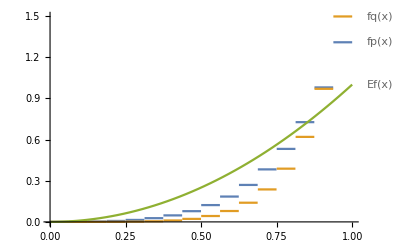

```mathematica
Plot[{fp[x],fq[x],Ef[x]},{x,0,1},PlotLabels-> "Expressions"]
```